### d)

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

{{0,-0.3},{0,-0.2},{0,-0.1},{0,5.55112×10^-17},{0,0.1},{0,0.2},{0,0.3}}

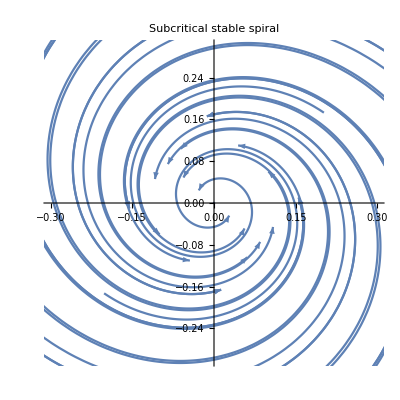

```mathematica
Clear["Global`*"]
xmin = -0.3;
xmax = 0.3;
ymin = -0.3;
ymax = 0.3;
solution[x0_, y0_]=NDSolve[{x'[t]==μ*x[t]-4 y[t]-x[t]^3,y'[t]==4 x[t]+μ*y[t]+2 y[t]^3,x[0]==x0,y[0]==y0}/. μ->-1,{x,y},{t,-1,1}];
IC0 = Table[{0,y},{y,ymin,ymax,0.1}]
IC1 = Table[{xmin, y}, {y,ymin, ymax, 0.2}];
IC2 = Table[{xmax, y},{y,ymin, ymax,0.2}];
IC3 = Table[{x,ymin},{x,xmin,xmax,0.2}];
IC4 = Table[{x,ymax},{x, xmin, xmax, 0.2}];
ICs = Join[IC0,IC1, IC2, IC3, IC4];
plot = 
Table[ParametricPlot[
Evaluate[{x[t],y[t]}/.solution[ICs[[i,1]],ICs[[i,2]]]],{t,-1,1}, PlotRange->{{xmin,xmax},{ymin,ymax}}, PlotLabel->"Subcritical stable spiral"]/. Line[x_]:>{Arrowheads[{0, 0.0375, 0.0375, 0}],Arrow[x]},{i,Length[ICs]}];
Show[{plot}]
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

{{0,-0.3},{0,-0.2},{0,-0.1},{0,5.55112×10^-17},{0,0.1},{0,0.2},{0,0.3}}

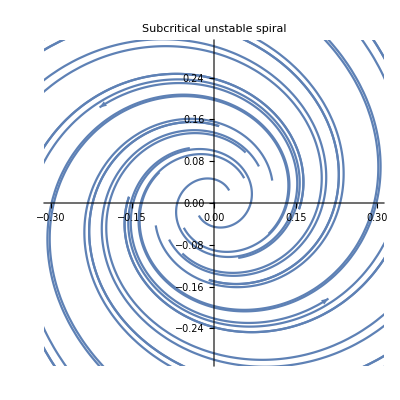

```mathematica
Clear["Global`*"]
Clear["Global`*"]
xmin = -0.3;
xmax = 0.3;
ymin = -0.3;
ymax = 0.3;
solution[x0_, y0_]=NDSolve[{x'[t]==μ*x[t]-4 y[t]-x[t]^3,y'[t]==4 x[t]+μ*y[t]+2 y[t]^3,x[0]==x0,y[0]==y0}/. μ->1,{x,y},{t,-1,1}];
IC0 = Table[{0,y},{y,ymin,ymax,0.1}]
IC1 = Table[{xmin, y}, {y,ymin, ymax, 0.2}];
IC2 = Table[{xmax, y},{y,ymin, ymax,0.2}];
IC3 = Table[{x,ymin},{x,xmin,xmax,0.2}];
IC4 = Table[{x,ymax},{x, xmin, xmax, 0.2}];
ICs = Join[IC0,IC1, IC2, IC3, IC4];
plot = 
Table[ParametricPlot[
Evaluate[{x[t],y[t]}/.solution[ICs[[i,1]],ICs[[i,2]]]],{t,-1,1}, PlotRange->{{xmin,xmax},{ymin,ymax}}, PlotLabel->"Subcritical unstable spiral"]/. Line[x_]:>{Arrowheads[{0, 0.0375, 0.0375, 0}],Arrow[x]},{i,Length[ICs]}];
Show[{plot}]
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

{{0,-0.3},{0,-0.2},{0,-0.1},{0,5.55112×10^-17},{0,0.1},{0,0.2},{0,0.3}}

NDSolve::ndsz: At t == -1.57494, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-1.99992} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -1.80563, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-1.99992} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == -1.75185, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

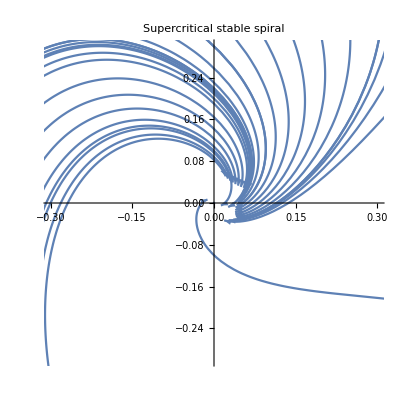

```mathematica
Clear["Global`*"]
xmin = -0.3;
xmax = 0.3;
ymin = -0.3;
ymax = 0.3;
solution[x0_, y0_]=NDSolve[{x'[t]==μ*x[t]+ y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0,y[0]==y0}/. μ->-1,{x,y},{t,-2,2}];
IC0 = Table[{0,y},{y,ymin,ymax,0.1}]
IC1 = Table[{xmin, y}, {y,ymin, ymax, 0.05}];
IC2 = Table[{xmax, y},{y,ymin, ymax,0.05}];
IC3 = Table[{x,ymin},{x,xmin,xmax,0.05}];
IC4 = Table[{x,ymax},{x, xmin, xmax, 0.05}];
ICs = Join[IC0,IC1, IC2, IC3, IC4];
plot = 
Table[ParametricPlot[
Evaluate[{x[t],y[t]}/.solution[ICs[[i,1]],ICs[[i,2]]]],{t,-2,2}, PlotRange->{{xmin,xmax},{ymin,ymax}}, PlotLabel->"Supercritical stable spiral"]/. Line[x_]:>{Arrowheads[{0, 0.0375, 0.0375, 0}],Arrow[x]},{i,Length[ICs]}];
Show[{plot}]
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

{{0,-0.3},{0,-0.2},{0,-0.1},{0,5.55112×10^-17},{0,0.1},{0,0.2},{0,0.3}}

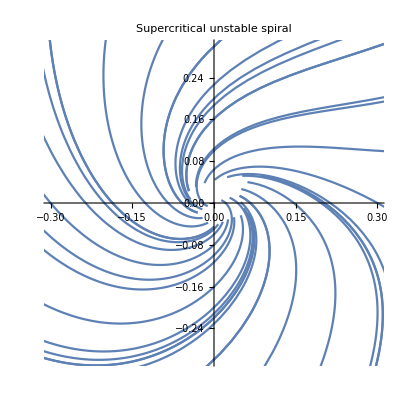

```mathematica
Clear["Global`*"]
xmin = -0.3;
xmax = 0.3;
ymin = -0.3;
ymax = 0.3;
solution[x0_, y0_]=NDSolve[{x'[t]==μ*x[t]+ y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0,y[0]==y0}/. μ->1,{x,y},{t,-2,2}];
IC0 = Table[{0,y},{y,ymin,ymax,0.1}]
IC1 = Table[{xmin, y}, {y,ymin, ymax, 0.1}];
IC2 = Table[{xmax, y},{y,ymin, ymax,0.1}];
IC3 = Table[{x,ymin},{x,xmin,xmax,0.1}];
IC4 = Table[{x,ymax},{x, xmin, xmax, 0.1}];
ICs = Join[IC0,IC1, IC2, IC3, IC4];
plot = 
Table[ParametricPlot[
Evaluate[{x[t],y[t]}/.solution[ICs[[i,1]],ICs[[i,2]]]],{t,-2,2}, PlotRange->{{xmin,xmax},{ymin,ymax}}, PlotLabel->"Supercritical unstable spiral"]/. Line[x_]:>{Arrowheads[{0, 0.0375, 0.0375, 0}],Arrow[x]},{i,Length[ICs]}];
Show[{plot}]
```